```mathematica
(*4.15*)
```

```mathematica
s=2;
xNodes=Table[Symbol["x"<>ToString[i]],{i,1,s+1}];
LagrangeBasis[i_,x_]:=Product[(x-xNodes[[j]])/(xNodes[[i]]-xNodes[[j]]),{j,DeleteCases[Range[1,s+1],i]}];
Ke=Table[Integrate[D[LagrangeBasis[i,x],x] D[LagrangeBasis[j,x],x],{x,xNodes[[1]],xNodes[[s+1]]}],{i,1,s+1},{j,1,s+1}];
fe=Table[Integrate[LagrangeBasis[i,x],{x,xNodes[[1]],xNodes[[s+1]]}],{i,1,s+1}];
KeSubstituted=Ke/. Thread[xNodes->Table[(i-1)/s,{i,1,s+1}]];
feSubstituted=fe/. Thread[xNodes->Table[(i-1)/s,{i,1,s+1}]];
KeSubstituted//MatrixForm
feSubstituted//MatrixForm
```

(7/3 | -8/3 | 1/3
-8/3 | 16/3 | -8/3
1/3 | -8/3 | 7/3)

(1/6
2/3
1/6)

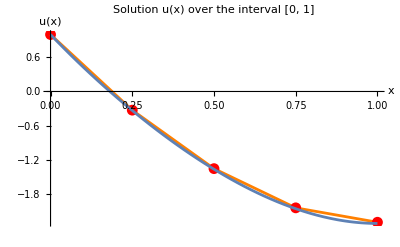

```mathematica
(*4.16*)
n=4; 
s=1; 
nodes=Table[i/n,{i,0,n}]; 
LagrangeBasis[i_,x_,xNodes_]:=Product[(x-xNodes[[j]])/(xNodes[[i]]-xNodes[[j]]),{j,DeleteCases[Range[1,Length[xNodes]],i]}];
a[x_]:=1+x;
f[x_]:=-18 x^2; 

KeElement[elementNodes_]:=Table[Integrate[a[x] D[LagrangeBasis[i,x,elementNodes],x] D[LagrangeBasis[j,x,elementNodes],x],{x,elementNodes[[1]],elementNodes[[2]]}],{i,1,s+1},{j,1,s+1}];
feElement[elementNodes_]:=Table[Integrate[f[x] LagrangeBasis[i,x,elementNodes],{x,elementNodes[[1]],elementNodes[[2]]}],{i,1,s+1}];
globalKe=ConstantArray[0,{n+1,n+1}];
globalFe=ConstantArray[0,n+1];
For[e=1,e<=n,e++,elementNodes={nodes[[e]],nodes[[e+1]]};
KeLocal=KeElement[elementNodes];
feLocal=feElement[elementNodes];
globalKe[[e;;e+s,e;;e+s]]+=KeLocal;
globalFe[[e;;e+s]]+=feLocal;
]

globalKe[[1,1]]=1;
globalKe[[1,2;;]]=0;
globalFe[[1]]=1;
u=LinearSolve[globalKe,globalFe];
plotu =ListLinePlot[Transpose[{nodes,u}],PlotRange->All,PlotLabel->"Solution u(x) over the interval [0, 1]",AxesLabel->{"x","u(x)"},PlotStyle->Orange,PlotStyle->Thick,Mesh->All,MeshStyle->Red];

deqn=-D[(1+x) D[c[x],x],x]==-18 x^2;
bc={c[0]==1,{D[c[x],x]/. x->1}==0};
exactSolution=DSolve[{deqn,bc},c[x],x];
realresult[p_] = c[x] /.exactSolution[[1]]; 
plotreal = Plot[realresult[x], {x, 0,1}];

Show[plotu, plotreal]
```